```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
Ds[n_,0,s_,a_]:=UnitStep[n-1]
Ds[n_,1,s_,a_]:=Ds[n,1,s,a]=HarmonicNumber[Floor[n],s]-HarmonicNumber[a,s]
Ds[n_,2,s_,a_]:=Ds[n,2,s,a]=Sum[(m^(-2s))+2(m^-s) (Ds[Floor[n/m],1,s,m]),{m,a+1,Floor[n^(1/2)]}]
Ds[n_,k_,s_,a_]:=Ds[n,k,s,a]=Sum[(m^(-s k))+k(m^(-s(k-1))) Ds[Floor[n/(m^(k-1))],1,s,m]+Sum[binomial[k,j] (m^-s)^j Ds[Floor[n/(m^j)],k-j,s,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]

Ddy[n_,s_,y_,k_]:=y^(k(s-1)) Ds[n y^k,k,s,y]
Ddy[0,s_,y_,k_]:=0

Dnsyz[n_,s_,y_,z_]:=Expand@Sum[binomial[z,k]Ddy[n,s,y,k],{k,0,Log[(y+1)/y,n]}]
d2[n_,y_,k_]:=Ddy[n,0,y,k]
dd[n_,y_,z_]:=Dnsyz[n,0,y,z]

ltod[ n_,y_, z_] := Sum[z^k/k! D[dd[n,y,t],{t,k}]/.t->0,{k,0,Log[(y+1)/y,n]}]
```

```mathematica
dd[100,2,z]
```

1+(202986703 z)/7096320+(68602319 z^2)/1612800+(622902011 z^3)/29030400+(2091660979 z^4)/371589120+(52801531 z^5)/74317824+(21461041 z^6)/353894400+(5689681 z^7)/2477260800+(16259 z^8)/247726080+(739 z^9)/743178240+(37 z^10)/7431782400+z^11/81749606400

```mathematica
D[dd[100,2,z],{z,2}]/.z->0
```

68602319/806400

```mathematica
ltod[10,16,3]
```

326425/4096

```mathematica
dd[10,16,3]
```

326425/4096

```mathematica
N@LaguerreL[-3,Log[10]]
```

82.5612

```mathematica
ff[n_, z_] := (-1)^z Gamma[z,0,-Log[n]]/Gamma[z]
Chop@N@Integrate[ ff[10/j,3.3],{j,1,10}]
```

-2.00791+6.17971 ⅈ

```mathematica
Chop@N@Gamma[4.3,0,-Log[10]]/Gamma[4.3]
```

3.81927+5.25678 ⅈ

```mathematica
Expand@Integrate[ 1,{x,1,n},{y,1,n/x}]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand@Integrate[n/x- 1,{x,1,n}]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand@Integrate[-Gamma[1,0,-Log[n/x]]/Gamma[1],{x,1,n}]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand@Integrate[-Gamma[2,0,-Log[n/(x y)]]/Gamma[2],{x,1,n},{y,1,n/x}]
```

ConditionalExpression[-1+n-n Log[n]+1/2 n Log[n]^2-1/6 n Log[n]^3,Re[n]≥0||n∉Reals]

```mathematica
Sum[ dd[100/j,2,2](dd[j,2,2]-dd[j-1,2,2]),{j,1,100}]
```

70469/16

```mathematica
dd[100,2,4]
```

37027/8

```mathematica
Sum[ (-1)^j (2j)!/((1-2j)(j!)^2(4^j)),{j,0,Infinity}]
```

√2

```mathematica
Clear[d2]
ex[j_]:=ex[j]=N[(-1)^(j-1) (2(j-1))!/((1-2(j-1))((j-1)!)^2(4^(j-1)))]
d2[n_, k_] := d2[n,k]=Sum[ ex[j] d2[Floor[n/j],k-1],{j,2,n}]
d2[n_, 0] := UnitStep[n-1]
dz[n_, z_] := Sum[ binomial[z,k]d2[n,k],{k,0,Log2@n}]
DzRoots[n_]:=If[(c=Exponent[f=dz[n,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
DzR[n_,z_]:=Chop@Expand@Product[1-z/rho,{rho,DzRoots[n]}]
```

```mathematica
Expand@N@dz[1000,z]
```

1.+0.346616 z+0.0600399 z^2+0.00684002 z^3+0.000729602 z^4-0.0000264379 z^5+0.0000210949 z^6-2.63562×10^-6 z^7+2.13441×10^-7 z^8-6.72786×10^-9 z^9

```mathematica
N@2^(1/2)
```

1.41421

```mathematica
N@Sum[ (-1)^j (2j)!/((1-2j)(j!)^2(4^j)),{j,2,100}]
```

-0.085927

```mathematica
N@(D[dz[1000,z],z]/.z->0)
```

0.346616

```mathematica
N@Log[2]/2
```

0.346574

```mathematica
DzRoots[1000]
```

{-3.77072-1.77362 ⅈ,-3.77072+1.77362 ⅈ,-1.82879-5.22551 ⅈ,-1.82879+5.22551 ⅈ,2.28265-8.308 ⅈ,2.28265+8.308 ⅈ,8.83877-10.1876 ⅈ,8.83877+10.1876 ⅈ,20.6812}

```mathematica
DzR[1000,4]
```

4.00002

```mathematica
N@Log[2^(1/2),77]
```

12.5336

```mathematica
DzR[10000,12.533573081389804]
```

76.9496

```mathematica
(2^(1/2))^z
```

2^(z/2)

```mathematica
Limit[ Sum[ (a-1)^s (-1)^s a^k k^(s-1),{k,1,Infinity}]/.s->1/2,a->1]
```

√π

```mathematica
Gamma[1/2+I]
```

Gamma[1/2+ⅈ]

```mathematica
Limit[Sum[ a-1,{k,0,Log[a,n]}],a->1]
```

Log[n]

```mathematica
ff[n_, a_] := Sum[ a-1,{k,0,Log[a,n]}]
f2[s_, b_] := Limit[ Sum[ (a-1)^s (-1)^s a^k k^(s-1),{k,0,Infinity}],a->b]
```

```mathematica
Plot[ f2[n,1],{n,.2,1}]
```

Power::infy: Infinite expression 1/0^0.799984 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NSum::nsnum: Summand (or its derivative) (0.808987  + 0.587827\ ⅈ)\ (-1 + a)^0.200016\ a^k/k^0.799984
 is not numerical at point k = 46661.

General::stop: Further output of NSum :: nsnum will be suppressed during this calculation.

$Aborted

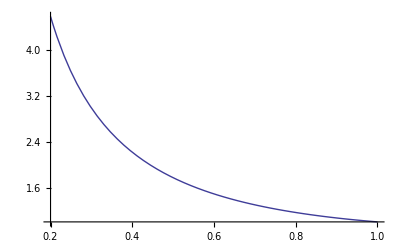

```mathematica
Plot[ Gamma[n],{n,.2,1}]
```

```mathematica
Limit[(LaguerreL[-z,Log[100.]]-1)/z,z->0]
```

28.0217

```mathematica
f2[n_, z_, a_] := (LaguerreL[a-z,Log[n]]-LaguerreL[a+z,Log[n]])/(2z)
f3[n_, z_] := (f2[n,z, -z]-f2[n,z,z])/(2z)
```

```mathematica
f2[100,.001,-.1]
```

36.7743

```mathematica
f3[100,.00001]
```

80.5038

```mathematica
g1[n_,0]:=1
g1[n_,a_] := Sum[ (-1)^k Gamma[k,0,-Log[n]]/Gamma[k](D[Log[1+x]^a,{x,k}]/.x->0)/k!,{k,1,80}]
gz[ n_, z_] := Sum[ z^k/k! g1[n,k],{k,0,40}]
```

```mathematica
Table[ Chop@N@g1[100,j],{j,0,40}]
```

{1.,28.0217,80.5038,134.883,162.645,154.116,120.57,80.4139,46.7678,24.1221,11.1796,4.70479,1.81335,0.644718,0.212737,0.0654893,0.0188938,0.00512882,0.00131459,0.000319152,0.0000735961,0.0000161607,3.38696×10^-6,6.78903×10^-7,1.30401×10^-7,2.40431×10^-8,4.26221×10^-9,7.27547×10^-10,1.19748×10^-10,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Chop@N@gz[100,-3+I]
```

4.28551+2.99377 ⅈ

```mathematica
N@LaguerreL[-(-3+I),Log[100]]
```

4.28551+2.99377 ⅈ

```mathematica
N@Integrate[ LaguerreL[-3,Log[100/x]],{x,1,100}]
```

4209.02

```mathematica
N@Integrate[ D[Gamma[2,0,-Log[j]]/Gamma[2],j]Gamma[2,0,-Log[100/j]]/Gamma[2],{j,1,100}]
```

928.88

```mathematica
Chop@Gamma[4,0,-Log[100.]]/Gamma[4]
```

928.88

```mathematica
N@Integrate[ D[Gamma[2,0,-Log[j]]/Gamma[2],j]Gamma[3,0,-Log[100/j]]/Gamma[3],{j,1,100}]
```

-945.128

```mathematica
N@Integrate[ D[Gamma[3,0,-Log[j]]/Gamma[3],j]Gamma[2,0,-Log[100/j]]/Gamma[2],{j,1,100}]
```

-945.128

```mathematica
N@Integrate[ D[(-1)^1 Gamma[1,0,-Log[j]]/Gamma[1],j](-1)^4 Gamma[4,0,-Log[100/j]]/Gamma[4],{j,1,100}]
```

945.128

```mathematica
Chop@((-1)^5 Gamma[5,0,-Log[100.]]/Gamma[5])
```

945.128

```mathematica
ff[n_, a_, b_] := Chop@N@Integrate[ D[(-1)^a Gamma[a,0,-Log[j]]/Gamma[a],j](-1)^b Gamma[b,0,-Log[n/j]]/Gamma[b],{j,1,n}]
f1[n_, a_, b_] := Chop@N@Integrate[ D[(-1)^a Gamma[a,0,-Log[j]]/Gamma[a],j]D[(-1)^b Gamma[b,0,-Log[k]]/Gamma[b],k],{j,1,n}, {k,1,n/j}]
f2[n_, a_, b_] := Chop@N@((-1)^(a+b) Gamma[a+b,0,-Log[n]]/Gamma[a+b])
```

```mathematica
ff[30,1,2+.3I]
```

15.4926+0.524826 ⅈ

```mathematica
f2[30,1,2+.3I]
```

15.4926+0.524826 ⅈ

```mathematica
f1[30,1,2+.3I]
```

15.4926+0.524826 ⅈ

```mathematica
N@Integrate[ D[LaguerreL[-3,Log[j]],j]LaguerreL[-1,Log[100/j]],{j,1,100}]
```

6190.43

```mathematica
N@LaguerreL[-4,Log[100]]
```

6290.43

```mathematica
D[ Gamma[1,0,-Log[x]],x]
```

-1

```mathematica
-b Integrate[ Gamma[ b, 0, -Log[n/x]],{x,1,n}]
```

ConditionalExpression[-b (-Gamma[b]+Gamma[b,-Log[n]]+(n (-Log[n])^b)/b),Re[b]>0&&(n∉Reals||Re[n]≥0)]

```mathematica
E^(-Log[n])
```

1/n

```mathematica
Limit[ Gamma[3,0,-Log[n]]/Gamma[3],n->Infinity]
```

-∞

```mathematica
gg[n_,z_] := (-1)^z Gamma[z,0,-Log[n]]/Gamma[z]
```

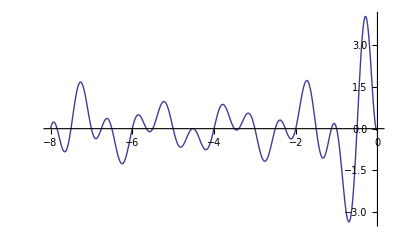

```mathematica
Plot[Im[gg[100,n]],{n,-8,0}]
```

```mathematica
gf[n_, a_, b_] := Chop@N@Integrate[ D[(-1)^(a+1) (Gamma[a,-Log[j]]/Gamma[a]),j]D[(-1)^(b+1) (Gamma[b,-Log[k]]/Gamma[b]),k],{j,1,n},{k,1,n/j}]
gf2[n_, a_, b_] := N[(-1)^(a+b)/(Gamma[a] Gamma[b])Integrate[ D[ (Gamma[a,-Log[j]]),j]D[ (Gamma[b,-Log[k]]),k],{j,1,n},{k,1,n/j}]]
g2[n_, a_, b_] := Chop@N@((-1)^(a+b)+(-1)^(a+b+1)(Gamma[a+b,-Log[n]]/Gamma[a+b]))
```

```mathematica
{gf[100,2.2,3],gf2[100,2.2,3],g2[100,2.2,3]}
```

{285.438+878.488 ⅈ,285.438+878.488 ⅈ,285.438+878.488 ⅈ}

```mathematica
hf2[n_, a_, b_] := N[(1/((-1)^(a+b+1)/Gamma[a+b]))(-(-1)^(a+b)+(-1)^(a+b)/(Gamma[a] Gamma[b])Integrate[ D[ (Gamma[a,-Log[j]]),j]D[ (Gamma[b,-Log[k]]),k],{j,1,n},{k,1,n/j}])]
hf3[n_, a_, b_] := N[Gamma[a+b]-Gamma[a+b]/(Gamma[a] Gamma[b])Integrate[ D[ (Gamma[a,-Log[j]]),j]D[ (Gamma[b,-Log[k]]),k],{j,1,n},{k,1,n/j}]]
h2[n_, a_, b_] := N@((Gamma[a+b,-Log[n]]))
```

```mathematica
{hf2[100,2.2,3],hf3[100,2.2,3],h2[100,2.2,3]}
```

{24377.8+17687.8 ⅈ,24377.8+17687.8 ⅈ,24377.8+17687.8 ⅈ}

```mathematica
Expand[ (1/((-1)^(a+b+1)/Gamma[a+b]))(-(-1)^(a+b)+(-1)^(a+b)/(Gamma[a] Gamma[b])VVV)]
```

Gamma[a+b]-(VVV Gamma[a+b])/(Gamma[a] Gamma[b])

```mathematica
gg[n_,z_] := (-1)^z Gamma[z,0,-Log[n]]/Gamma[z]
hh[n_,z_] :=  (Log[n])^(z-1)/Gamma[z]
```

```mathematica
D[gg[n,z],n]/.z->2
```

Log[n]

```mathematica
Expand@Integrate[ Log[a]Log[b],{a,1,n},{b,1,n/a}]
```

ConditionalExpression[1-n+n Log[n]-1/2 n Log[n]^2+1/6 n Log[n]^3,Re[n]≥0||n∉Reals]

```mathematica
FullSimplify@Integrate[ hh[a,z],{a,1,n}]
```

ConditionalExpression[((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/Gamma[z],Re[z]>0]

```mathematica
((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/Gamma[z]
```

((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/Gamma[z]

```mathematica
N@gg[100,3.25]
```

-7.95808×10^-13+772.957 ⅈ

```mathematica
tt[ n_, z_] := N@Sum[(-1)^(k) Binomial[z,k] LaguerreL[-k,Log[n]],{k,0,40}]
```

```mathematica
(-1)^(5)Chop@N@Gamma[5,0,-Log[10]]/Gamma[5]
```

3.84941

```mathematica
tt[10,5]
```

-3.84941

```mathematica
N@D[LaguerreL[-3,Log[n]],{n,2}]/.n->100
```

0.0760517

```mathematica
N@Sum[ D[ Binomial[ 3,k](((-1)^k Gamma[k,0,-Log[n]]/Gamma[k])),{n,2}],{k,1,4}]/.n->100
```

0.0760517

```mathematica
FullSimplify@Sum[ Binomial[ a,k]Binomial[b,j-k],{k,0,j}]
```

Binomial[a+b,j]

```mathematica
Binomial[a+b,5]
```

1/120 (-4+a+b) (-3+a+b) (-2+a+b) (-1+a+b) (a+b)

```mathematica
N@Integrate[ D[ LaguerreL[-1,Log[a]],a] D[ LaguerreL[-4,Log[b]],b],{a,1,10},{b,1,10/a}]
```

166.307

```mathematica
LaguerreL[-5,Log[10.]]
```

354.26

```mathematica
aa[x_,z_] := x^z
```

```mathematica
D[aa[x,1],x]
```

1

```mathematica
Integrate[ D[aa[x,1.5+I],x]D[aa[y,1],y],{x,0,10},{y,0,10}]
```

-211.304+235.267 ⅈ

```mathematica
aa[10,3.5+I]
```

-2113.04+2352.67 ⅈ

```mathematica
Integrate[ D[x^(1.5+I),x]D[y^2,y],{x,0,10},{y,0,10}]
```

-2113.04+2352.67 ⅈ

```mathematica
aff[n_, a_] := (-1)^a Gamma[a,0,-Log[n]]/Gamma[a]
aff[n_,0] := Limit[ (-1)^a Gamma[a,0,-Log[n]]/Gamma[a],a->0]
af[n_, s_, a_] := (-1)^a Gamma[a,0,(s-1)Log[n]]/Gamma[a]
a1[n_, s_, a_, b_] := Chop@N@Integrate[ D[af[j,s,a],j]D[af[k,s,b],k],{j,1,n}, {k,1,n/j}]
a2[n_, s_, a_, b_] := Chop@N@(af[n,s,a+b])
aaa[n_, z_] := (-1)^z Sum[ (-1)^k Binomial[z,k]aff[n,k],{k,0,120}]
aaa2[n_, z_] := (-1)^z Sum[ (-1)^k Binomial[z,k]aff[n,k],{k,0,Infinity}]
aab[n_, z_] := Chop@N[ Sum[  Binomial[z,k]aff[n,k],{k,0,120}]]
```

```mathematica
a1[100,0,.5,1.5]
```

361.517

```mathematica
a2[100,0,1,1]
```

361.517

```mathematica
Table[ N@aaa[100,k]/k,{k,1,20}]
```

{98.,82.2585-2.20753×10^-14 ⅈ,-29.8962-1.29884×10^-14 ⅈ,-23.117+1.99666×10^-14 ⅈ,33.6365-2.93797×10^-14 ⅈ,-17.3605+9.18606×10^-14 ⅈ,-3.59917-2.49128×10^-13 ⅈ,16.4263+5.31436×10^-13 ⅈ,-18.1963-9.62693×10^-13 ⅈ,11.9096+1.5656×10^-12 ⅈ,-2.48172-2.37613×10^-12 ⅈ,-5.8531+3.51323×10^-12 ⅈ,10.655-5.41806×10^-12 ⅈ,-11.3375+9.48482×10^-12 ⅈ,8.66831-1.94566×10^-11 ⅈ,-4.10328+4.41531×10^-11 ⅈ,-0.804403-1.02326×10^-10 ⅈ,4.80809+2.30686×10^-10 ⅈ,-7.16442-4.96401×10^-10 ⅈ,7.65696+1.01559×10^-9 ⅈ}

```mathematica
N@LaguerreL[-10,Log[100]]
```

780182.

```mathematica
aaa[100,0]+4 aaa[100,1]+6aaa[100,2]+4aaa[100,3]+aaa[100,4]
```

928.88

```mathematica
N@aff[100,4]
```

928.88-3.40898×10^-13 ⅈ

```mathematica
ff5[ n_, z_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
ff5a[ n_, z_] := Integrate[Sum[(-1)^k Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
```

```mathematica
LaguerreL[-2,Log[n]]/.n->100
```

LaguerreL[-2,Log[100]]

```mathematica
N[((aff[100,bb])-(aff[100,-bb]))/(2bb)/.bb->.00001]
```

30.1261+6.28319 ⅈ

```mathematica
Gamma[0,-Log[100.]]
```

-30.1261-3.14159 ⅈ

```mathematica
Residue[ aff[100., z]/z^2, {z,0}]
```

Residue[((-1)^z Gamma[z,0,-4.60517])/(z^2 Gamma[z]),{z,0}]

```mathematica
N[((LaguerreL[-3,Log[100+bb]])-(LaguerreL[-3, Log[100-bb]]))/(2bb)/.bb->.000001]
```

27.4193

```mathematica
D[ LaguerreL[-3, Log[n]],n]/.n->100.
```

27.4193

```mathematica
N@Integrate[ D[LaguerreL[-1,Log[j]],j]D[LaguerreL[-3,Log[k]],k],{j,1,10}, {k,1,10/j}]+LaguerreL[-1,Log[10]]+LaguerreL[-3,Log[10]]-1
```

178.953

```mathematica
N@Integrate[ D[LaguerreL[-2,Log[j]],j]D[LaguerreL[-2,Log[k]],k],{j,1,10}, {k,1,10/j}]+LaguerreL[-2,Log[10]]+LaguerreL[-2,Log[10]]-1
```

178.953

```mathematica
N@LaguerreL[-4,Log[10]]
```

178.953

```mathematica
N@Integrate[ D[LaguerreL[-2,Log[j]],j]D[LaguerreL[-3,Log[k]],k],{j,1,10}, {k,1,10/j}]+LaguerreL[-2,Log[10]]+LaguerreL[-3,Log[10]]-1
```

354.26

```mathematica
N@Integrate[ D[LaguerreL[-.75,Log[j]],j]D[LaguerreL[4.5,Log[k]],k],{j,1,10}, {k,1,10/j}]+LaguerreL[-.75,Log[10]]+LaguerreL[4.5,Log[10]]-1
```

0.591448

```mathematica
N@Integrate[ D[LaguerreL[-.75,Log[j]],j]D[LaguerreL[4.5,Log[k]],k],{j,1,10}, {k,1,10/j}]+LaguerreL[-.75,Log[10]]+LaguerreL[4.5,Log[10]]-1
```

0.591448

```mathematica
N@LaguerreL[4.5-.75,Log[10]]
```

0.591448

```mathematica
N[D[LaguerreL[-1,Log[n]],n]/.n->100]
```

1.

```mathematica
Gamma[3,0,-Log[10]]/Gamma[3]-3Gamma[2,0,-Log[10]]/Gamma[2]+3Gamma[1,0,-Log[10]]/Gamma[1]-1
```

-28-3 Gamma[2,0,-Log[10]]+1/2 Gamma[3,0,-Log[10]]

```mathematica
N@Gamma[3,0,-Log[10]]
```

-24.9673+9.17283×10^-15 ⅈ

```mathematica
N@-2(10Log[10]^2/2-10Log[10]+10-1)
```

-24.9673

```mathematica
N@Gamma[2,0,-Log[10]]
```

14.0259-1.59521×10^-15 ⅈ

```mathematica
N@(10Log[10]-10+1)
```

14.0259

```mathematica
N@Gamma[1,0,-Log[10]]
```

-9.

```mathematica
Sum[ Binomial[z,k] (-1)^(k+1) (-Log[ x] )^(k-1)/Gamma[k],{k,0,Infinity}]
```

z Hypergeometric1F1[1-z,2,-Log[x]]

```mathematica
N[z Hypergeometric1F1[1-z,2,-Log[x]]/.{x->100,z->3}]
```

27.4193

```mathematica
D[ LaguerreL[-3, Log[n]],n]/.n->100.
```

27.4193

```mathematica
Integrate[ (2 Hypergeometric1F1[1-2,2,-Log[x]])(3 Hypergeometric1F1[1-3,2,-Log[y]]),{x,1,n},{y,1,n/x}]
```

ConditionalExpression[1/2 (2-2 n+1/12 n Log[n] (24+Log[n] (6+Log[n]) (10+Log[n]))),Re[n]≥0||n∉Reals]

```mathematica
Integrate[ (4Hypergeometric1F1[1-4,2,-Log[x]])(3 Hypergeometric1F1[1-3,2,-Log[y]]),{x,1,n},{y,1,n/x}]
```

ConditionalExpression[1/12 (-12 (-1+n)+1/60 n Log[n] (720+Log[n] (6+Log[n]) (660+Log[n] (270+Log[n] (30+Log[n]))))),Re[n]≥0||n∉Reals]

```mathematica
Integrate[ (5Hypergeometric1F1[1-5,2,-Log[x]])(2 Hypergeometric1F1[1-2,2,-Log[y]]),{x,1,n},{y,1,n/x}]
```

ConditionalExpression[1/24 (-24 (-1+n)+1/30 n Log[n] (720+Log[n] (3240+Log[n] (1920+Log[n] (420+Log[n] (36+Log[n])))))),Re[n]≥0||n∉Reals]

```mathematica
ar[n_, a_] := (-1)^a Gamma[a,0,-Log[n]]/Gamma[a]
ar2[n_, a_] := Gamma[a,0,-Log[n]]/Gamma[a]
ar3[n_, a_] := Gamma[a,0,Log[n]]/Gamma[a]
ar4[x_, z_] := Gamma[z,0,(s-1)Log[x]]/Gamma[z]
ar5[x_, z_] := (-1)^z Gamma[z,0,(s-1)Log[x]]/Gamma[z]
```

```mathematica
FullSimplify[D[ar4[x,z],x]]
```

(x^-s ((-1+s) Log[x])^z)/(Gamma[z] Log[x])

```mathematica
FullSimplify[D[ar5[x,z],x]]
```

((-1)^z x^-s ((-1+s) Log[x])^z)/(Gamma[z] Log[x])

```mathematica
D[ar[n,a],n]/.a->1
```

1

```mathematica
FullSimplify[D[Gamma[ a,0,-Log[x]],x]]
```

(-Log[x])^a/Log[x]

```mathematica
ff5[ n_, z_] := Integrate[Sum[ Binomial[z,k] (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
ff5b[ n_, z_] := Integrate[Sum[z^k/k! (-1)^(k+1)/((k-1)!) t^(k-1)E^(-t),{k,0, Infinity}],{t,-Log[n],0}]
ff5c[ n_, z_] := Sum[z^k/k! (-1)^k ( 1 - Gamma[ k, -Log[n]]/Gamma[k]),{k,0, Infinity}]
ff5d[ n_, z_] := Sum[(-1)^k z^(2k)/(2k)! (-1)^(2k) ( 1 - Gamma[ 2k, -Log[n]]/Gamma[2k]),{k,0, Infinity}]
ff5e[ n_, z_,t_] := Sum[(-1)^k z^(2k)/(2k)! (-1)^(2k) ( 1 - Gamma[2 k, -Log[n]]/Gamma[2k]),{k,0, t}]
```

```mathematica
ff5b[100,1]
```

∫_(-Log[100])^0 (ⅇ^-t BesselJ[1,2 √t])/(√t)ⅆt

```mathematica
ff5c[100,1]
```

∑_(k=0)^∞ ((-1)^k (1-Gamma[k,-Log[100]]/Gamma[k]))/(k!)

```mathematica
ff5d[100,1]
```

∑_(k=0)^∞ ((-1)^(3 k) (1-Gamma[2 k,-Log[100]]/Gamma[2 k]))/((2 k)!)

```mathematica
N@ff5e[10,1,30]
```

-5.68744+6.38683×10^-16 ⅈ

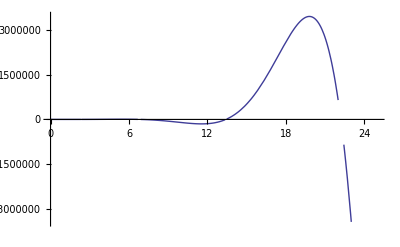

```mathematica
Plot[ ff5e[100,z,30],{z,0,25}]
```

```mathematica
Integrate[ 1,{x,1,n}]
```

-1+n

```mathematica
Expand@Integrate[ 1,{x,1,n},{y,1,n/x}]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand@Integrate[ 1,{x,1,n},{y,1,n/x}, {z,1,n/(x y)}]
```

ConditionalExpression[-1+n-n Log[n]+1/2 n Log[n]^2,Re[n]≥0||n∉Reals]

```mathematica
N@(-1)^2 Gamma[2,0,-Log[100]]/Gamma[2]
```

361.517-4.41506×10^-14 ⅈ

```mathematica
N[(n Log[n] - n + 1)/.n->100]
```

361.517

```mathematica
FullSimplify@Sum[ z^k/k! (-1)^k, {k,1,Infinity}]
```

-1+ⅇ^-z

```mathematica
FullSimplify@Sum[ z^k/k! (-1)^(k+1) n, {k,2,Infinity}]
```

-n (-1+ⅇ^-z+z)

```mathematica
FullSimplify@Sum[ z^k/k! (-1)^(k+0) n Log[n], {k,3,Infinity}]
```

-1/2 n Log[n] (2+(-2+z) z-2 Cosh[z]+2 Sinh[z])

```mathematica
FullSimplify@Sum[ z^k/k! (-1)^(k+1) n Log[n]^2/2, {k,4,Infinity}]
```

1/12 ⅇ^-z n (-6+ⅇ^z (6-z (6+(-3+z) z))) Log[n]^2

```mathematica
FullSimplify@Sum[ z^k/k! (-1)^(k+0) n Log[n]^3/6, {k,5,Infinity}]/.z->3
```

((24-33 ⅇ^3) n Log[n]^3)/(144 ⅇ^3)

```mathematica
Table[ Cos[Pi/2 j],{j,0,10}]
```

{1,0,-1,0,1,0,-1,0,1,0,-1}

```mathematica
Integrate[ D[ LaguerreL[-z,Log[x]],x],{x,0,n}]
```

ConditionalExpression[LaguerreL[-z,Log[n]],Re[z]>0&&(n∉Reals||Re[n]≤ⅇ)]

```mathematica
Integrate[ D[ LaguerreL[-z,Log[x]],x],{x,1,n}]
```

ConditionalExpression[-1+Hypergeometric1F1[z,1,Log[n]],0≤Re[n]≤ⅇ||n∉Reals]

```mathematica
N@Integrate[ D[LaguerreL[-.75,Log[j]],j]D[LaguerreL[-4.5,Log[k]],k],{j,1,10}, {k,1,10/j}]+LaguerreL[-.75,Log[10]]+LaguerreL[-4.5,Log[10]]-1
```

415.707

```mathematica
N@Integrate[ D[LaguerreL[-.75,Log[j]],j]Integrate[ D[LaguerreL[-4.5,Log[k]],k],{k,1,10/j}],{j,1,10}]+LaguerreL[-.75,Log[10]]+LaguerreL[-4.5,Log[10]]-1
```

415.707

```mathematica
Integrate[ D[LaguerreL[z,Log[k]],k],{k,1,n/j}]
```

ConditionalExpression[-1+LaguerreL[z,Log[n/j]],(n/j∉Reals||(Re[n/j]≥0&&(j^2≠j n||Re[n/j]≤1)))&&((Re[j]≠0&&Im[n]≠(Im[j] Re[n])/Re[j])||(Re[j]>0&&Re[n]≥0)||(Re[j]<0&&Re[n]≤0)||(Re[j]==0&&((j∉Reals&&Re[n]≠0)||(Re[n]==0&&((Im[j]>0&&Im[n]≥0)||(Im[j]<0&&Im[n]≤0))))))]

```mathematica
Integrate[ D[LaguerreL[z,Log[k]],k],{k,0,n/j}]
```

ConditionalExpression[LaguerreL[z,Log[n/j]],Re[z]<0]

```mathematica
Integrate[ D[LaguerreL[-2,Log[k]],k],{k,0,10/j}]
```

(10 (1+Log[10]+Log[1/j]))/j

```mathematica
N@Integrate[ D[LaguerreL[-.75,Log[j]],j]Integrate[ D[LaguerreL[-4.5,Log[k]],k],{k,1,10/j}],{j,1,10}]+LaguerreL[-.75,Log[10]]+LaguerreL[-4.5,Log[10]]-1
```

415.707

```mathematica
N@Integrate[ D[LaguerreL[-.75,(-2+I)Log[j]],j](-1+LaguerreL[-4.5,(-2+I)Log[10/j]]),{j,1,10}]+LaguerreL[-.75,(-2+I)Log[10]]+LaguerreL[-4.5,(-2+I)Log[10]]-1
```

-0.0923407-0.0296361 ⅈ

```mathematica
LaguerreL[-.75-4.5,(-2+I)Log[10]]
```

-0.0923407-0.0296361 ⅈ

```mathematica
s=.5+I;t=.3+2I;x=20;l=2-I;
N[Gamma[s+t,0,l Log[x]]]
N[Gamma[s+t]/(Gamma[s]Gamma[t])Integrate[ D[Gamma[s,0, l Log[y]],y](Gamma[t,0,l Log[x/y]]),{y,1,x}]]
```

0.0277866+0.0198951 ⅈ

0.0277866+0.0198951 ⅈ

```mathematica
s=.5+I;t=.3+2I;x=20;l=2-I;
N[Gamma[s+t,l Log[x]]]
N[Gamma[s+t]-Gamma[s+t]/(Gamma[s]Gamma[t])Integrate[ D[Gamma[s, l Log[y]],y](D[Gamma[t,l Log[z]],z]),{y,1,x},{z,1,x/y}]]
```

-0.00524201+0.00178877 ⅈ

-0.00524201+0.00178877 ⅈ

```mathematica
Clear[x,a,b,y,n,z,u,t,l]
FullSimplify[Integrate[ D[Gamma[t,l Log[z]],z],{z,1,n/y}]]
FullSimplify[Integrate[ D[Gamma[t,0,l Log[z]],z],{z,1,n/y}]]
```

ConditionalExpression[-Gamma[t]+Gamma[t,l Log[n/y]],Re[t]>0&&Log[n/y]>0]

ConditionalExpression[Gamma[t]-Gamma[t,l Log[n/y]],Re[t]>0&&Log[n/y]>0]

```mathematica
Clear[x,a,b,y,n,z,u,t]
Integrate[ D[y^t,y]D[z^u,z],{y,0,x},{z,0,x}]
```

ConditionalExpression[x^(t+u),Re[t]>0]

```mathematica
N[-Gamma[t]+Gamma[t,l Log[n/y]]/.{t->3,l->-1,n->100,y->1}]
```

1397.73-3.42834×10^-13 ⅈ

```mathematica
N[Gamma[t]-Gamma[t,l Log[n/y]]/.{t->3,l->-1,n->100,y->1}]
```

-1397.73+3.42834×10^-13 ⅈ

```mathematica
Clear[x, b, n]
-b Integrate[ Gamma[ b, 0, -Log[n]+Log[x]],{x,1,n}]
```

ConditionalExpression[-b (-Gamma[b]+Gamma[b,-Log[n]]+(n (-Log[n])^b)/b),Re[b]>-1&&(n∉Reals||Re[n]≥0)]

```mathematica
Chop@N@Gamma[6,0,-Log[20]]
```

1665.96

```mathematica
E^-(-Log[n])
```

n

```mathematica
Limit[D[Gamma[k,0,-Log[n]],n],k->0]
```

1/Log[n]

```mathematica
Plot[ Gamma[0,0,-Log[n]],{n,1,10}]
```

-Graphics-

```mathematica
N@Gamma[0,-Log[100]]
```

-30.1261-3.14159 ⅈ

```mathematica
Limit[(LaguerreL[s,-Log[n]]-1)/s,s->0]
```

LaguerreL^(1,0)[0,-Log[n]]

```mathematica
D[Derivative[1,0][LaguerreL][0,-Log[n]],n]
```

-(LaguerreL^(1,1)[0,-Log[n]])/n

```mathematica
D[ Gamma[k,0,-Log[n]],n]/.k->0
```

1/Log[n]

```mathematica
Sum[ Binomial[ z,k] (-1)^(k+1) (-Log[n])^(k-1)/Gamma[k],{k,0,Infinity}]
```

z Hypergeometric1F1[1-z,2,-Log[n]]

```mathematica
N[D[LaguerreL[-z,Log[n]],n]/.{n->10,z->-3}]
```

0.125681

```mathematica
N[D[LaguerreL[-z,Log[n]],z]/.{n->100,z->0}]
```

28.0217

```mathematica
D[ Gamma[k,-Log[10]],k]
```

Gamma[k,-Log[10]] (ⅈ π+Log[Log[10]])+MeijerG[{{},{1,1}},{{0,0,k},{}},-Log[10]]

```mathematica
D[LaguerreL[-z, Log[n]],n]
```

-LaguerreL[-1-z,1,Log[n]]/n

```mathematica
Integrate[ D[ LaguerreL[-z,Log[y]],y],{y,0,x}]
```

ConditionalExpression[LaguerreL[-z,Log[x]],Re[z]>0&&(x∉Reals||Re[x]≤ⅇ)]

```mathematica
Clear[ck]
ck[n_, s_, k_] := ck[n,s,k]=Sum[ j^-s ck[ n,s,k-1],{j,1,n}]
ck[n_, s_, 0] := 1
cz[n_, s_, z_] := Sum[ Binomial[ z,k]ck[n,s,k],{k,0,Infinity}]
```

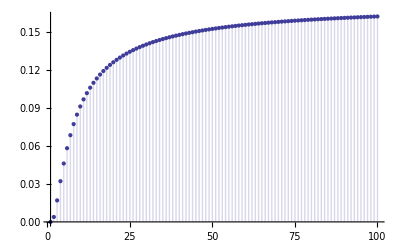

```mathematica
DiscretePlot[ ck[n,2,4],{n,1,100}]
```

```mathematica
ck[20,0,5]
```

3200000

```mathematica
Sum[ (ck[j,0,2]-ck[j-1,0,2])ck[20,0,3],{j,1,20}]
```

3200000

```mathematica
Sum[ (j k l)^1,{j,2,n},{k,2,n},{l,2,n}]
```

1/8 (-2+n+n^2)^3

```mathematica
Integrate[ j^-s, {j,1,x}]
```

ConditionalExpression[(x^-s (-x+x^s))/(-1+s),Re[x]≥0||x∉Reals]

```mathematica
Integrate[ (j k)^-s, {j,1,x},{k,1,x}]
```

ConditionalExpression[(x^(-2 s) (-x+x^s)^2)/(-1+s)^2,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@Integrate[ (j k l)^-s, {j,1,x},{k,1,x},{l,1,x}]
```

ConditionalExpression[(x^(-3 s) (-x+x^s)^3)/(-1+s)^3,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@Integrate[ (j k l m)^-s, {j,1,x},{k,1,x},{l,1,x}, {m,1,x}]
```

ConditionalExpression[(x^(-4 s) (-x+x^s)^4)/(-1+s)^4,Re[x]≥0||x∉Reals]

```mathematica
FullSimplify@Sum[ Binomial[z,k](x^(-k s) (-x+x^s)^k)/(-1+s)^k,{k,0,Infinity}]
```

((x^-s (-x+s x^s))/(-1+s))^z

```mathematica
Expand[((x^-s (-x+s x^s))/(-1+s))^z]
```

((x^-s (-x+s x^s))/(-1+s))^z

```mathematica
Expand[x^-s (-x+s x^s)]
```

s-x^(1-s)

```mathematica
FullSimplify[(s-x^(1-s))/(-1+s)]
```

(s-x^(1-s))/(-1+s)

```mathematica
6^4
```

```mathematica
Clear[ee] 
ee[n_, 1] := Sum[ PrimePi[ n^(1/k)]/k,{k,1,Log2@n}]
ee[n_, k_] := ee[n,k]=If[ n<=k,0,ee[n,k-1]-ee[n-1,k-1]]
ee[0,1]:=0
ee[0,k_]:=0
Table[ ee[n,k],{n,1,12},{k,1,12}]//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5/2 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7/2 | 1 | 1/2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7/2 | 0 | -1 | -3/2 | -5/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9/2 | 1 | 1 | 2 | 7/2 | 6 | 0 | 0 | 0 | 0 | 0 | 0
29/6 | 1/3 | -2/3 | -5/3 | -11/3 | -43/6 | -79/6 | 0 | 0 | 0 | 0 | 0
16/3 | 1/2 | 1/6 | 5/6 | 5/2 | 37/6 | 40/3 | 53/2 | 0 | 0 | 0 | 0
16/3 | 0 | -1/2 | -2/3 | -3/2 | -4 | -61/6 | -47/2 | -50 | 0 | 0 | 0
19/3 | 1 | 1 | 3/2 | 13/6 | 11/3 | 23/3 | 107/6 | 124/3 | 274/3 | 0 | 0
19/3 | 0 | -1 | -2 | -7/2 | -17/3 | -28/3 | -17 | -209/6 | -457/6 | -335/2 | 0

```mathematica
Table[ ee[n,n-1],{n,2,12}]
```

{1,1,-1/2,1,-5/2,6,-79/6,53/2,-50,274/3,-335/2}

```mathematica
9/2 +1/3
```

29/6

```mathematica
29/6+1/2
```

16/3

```mathematica
1/6 - (-2/3)
```

5/6

```mathematica
-1/2 - 1/6
```

-2/3

```mathematica
pp[x_,s_,z_]:=((s-x^(1-s))/(-1+s))^z
```

```mathematica
pp[10,0,-2]
```

1/100

```mathematica
D[pp[x,s,z],z]/.{z->0,s->0}
```

Log[x]

```mathematica
(s-x^(1-s))/(-1+s)
```

```mathematica
(s-x^(1-s))/(-1+s)/.{x->3,s->2}
```

5/3

```mathematica
(-s+x^(1-s))/(1-s)
```

(-s+x^(1-s))/(1-s)

```mathematica
N[Integrate[ D[ LaguerreL[-2,Log[j]],j] D[LaguerreL[-3,Log[k]],k],{j,1,20},{k,1,20/j}]+LaguerreL[-2,Log[20]]+LaguerreL[-3,Log[20]]-1]
```

1223.71

```mathematica
N[LaguerreL[-5,Log@20]]
```

1223.71

```mathematica
N[Integrate[ D[ LaguerreL[-2,Log[j]],j] D[LaguerreL[-3,Log[k]],k],{j,.125,20},{k,.125,20/j}]]
```

1608.3

```mathematica
Integrate[ D[ LaguerreL[-3/2,Log[j]],j],{j,1,20}]
```

-1+LaguerreL[-3/2,Log[20]]